The following equation represents the continuous topography of a mountainous region, giving the elevation h at any point {x,y}:

-Graphics-

A mosquito intends to fly from A{200,200} to B{1400,1400}, without leaving the area given by 0≤x≤1600,0≤y≤1600.

Because of the intervening mountains, it first rises straight up to a point A’, having elevation f. Then, while remaining at the same elevation f, it flies around any obstacles until it arrives at a point B’ directly above B.

First, determine f_min which is the minimum constant elevation allowing such a trip from A to B, while remaining in the specified area.
Then, find the length of the shortest path between A’ and B’, while flying at that constant elevation f_min.

Give that length as your answer, rounded to three decimal places.

Note: For convenience, the elevation function shown above is repeated below, in a form suitable for most programming languages:
h=(5000-0.005*(x*x+y*y+x*y)+12.5*(x+y))*exp(-abs(0.000001*(x*x+y*y)-0.0015*(x+y)+0.7))

如下的等式表示了一座山连续的地貌，对于任意一点{x,y}，其海拔h为：

-Graphics-

一只蚊子试图从点A{200,200}飞往点B{1400,1400}，但不能离开0≤x≤1600,0≤y≤1600的这片区域。

为了避免地貌的影响，它先竖直向上飞到一点A’，其海拔为f。然后，它保持海拔高度f不变，绕过所有障碍，直到它到达B点正上方的一点B’。

首先，找出在给定区域内存在由A至B路径的最小海拔高度f_min。
其次，找出A’到B’的最短路径长度，路径上的海拔高度始终为常数f_min。

给出最短路径长度并四舍五入至三位小数作为你的答案。

注意：方便起见，上述海拔函数在下面按照方便大多数编程语言习惯的方式重写为：
h=(5000-0.005*(x*x+y*y+x*y)+12.5*(x+y))*exp(-abs(0.000001*(x*x+y*y)-0.0015*(x+y)+0.7))

g[x,y]=(x^2+y^2)/1000000-(3 (x+y))/2000+7/10
当{x,y}∈𝒟时，g[x,y]>0
当{x,y}∈𝒞时，g[x,y]==0
𝒟=ImplicitRegion[(x-750)^2+(y-750)^2>425000,{x,y}]
𝒞=ImplicitRegion[(x-750)^2+(y-750)^2==425000,{x,y}]
h[x,y]=Piecewise[{{(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^(-g[x,y]), {x,y}∈𝒟}, {(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^g[x,y], True}}]
h^(1,0)[x,y]=Piecewise[{{(-(2 x+y)/200+25/2+(-x/500000+3/2000) (5000-(x^2+y^2+x y)/200+(25 (x+y))/2)) ⅇ^(-g[x,y]), {x,y}∈𝒟}, {Indeterminate, {x,y}∈𝒞}, {(-(2 x+y)/200+25/2+(x/500000-3/2000) (5000-(x^2+y^2+x y)/200+(25 (x+y))/2)) ⅇ^g[x,y], True}}]
h^(0,1)[x,y]=Piecewise[{{(-(2 y+x)/200+25/2+(-y/500000+3/2000) (5000-(x^2+y^2+x y)/200+(25 (x+y))/2)) ⅇ^(-g[x,y]), {x,y}∈𝒟}, {Indeterminate, {x,y}∈𝒞}, {(-(2 y+x)/200+25/2+(y/500000-3/2000) (5000-(x^2+y^2+x y)/200+(25 (x+y))/2)) ⅇ^g[x,y], True}}]
h[x,y]在{x,y}={1600,1600}处有最小值 6600/ⅇ^(51/50)，在{x,y}={2000/3,2000/3}处有极小值 15000/ⅇ^(37/90)，在{x,y}={875-75 √35,875+75 √35}或{875+75 √35,875-75 √35}处有最大值 57625/4
∀400≤t≤2800,有蚊子的路径必然与直线x+y=t有公共点
i[t]=MinValue[{h[x,t-x],0≤x≤1600,0≤t-x≤1600},x]=Piecewise[{{(5000-t^2/200+(25 t)/2) ⅇ^(-(t^2/1000000-(3 t)/2000+7/10)), 400≤t<1600}, {(-7800-t^2/200+(41 t)/2) ⅇ^(-(t^2/1000000-(47 t)/10000+291/50)), 1600≤t≤2800}}]
经检验，i[t]是连续函数，i[t]在t=Root[2000000000-125000 #1-3250 #1^2+#1^3&,2]处有最大值f_min
f_min=Root[-640625000000-206250000 #1-3125 #1^2+2 #1^3&,3] ⅇ^Root[8172+56505 #1+32150 #1^2+4000 #1^3&,3]
根据图像，蚊子的最短路径由以下三个部分组成：
由(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^(-((x^2+y^2)/1000000-(3 (x+y))/2000+7/10))=f_min 确定的曲线的经过点A{200,200}的切线，切点为C{xc,yc}，其中yc<xc；
由(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^(-((x^2+y^2)/1000000-(3 (x+y))/2000+7/10))=f_min 确定的曲线的经过点B{1400,1400}的切线，切点为D{xd,yd}，其中yd<xd；
由(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^(-((x^2+y^2)/1000000-(3 (x+y))/2000+7/10))=f_min 确定的劣曲线CD

```mathematica
h[x_,y_]:=(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^(-Abs[(x^2+y^2)/1000000-(3 (x+y))/2000+7/10]);
Plot3D[h[x,y],{x,0,1600},{y,0,1600},AxesLabel->Automatic,MaxRecursion->4,PlotPoints->50]
```

-Graphics3D-

```mathematica
{xc,yc}={xc,yc}/.FindRoot[{yc-200==(-2000000000+125000 xc+3250 xc^2-xc^3-1375000 yc+3250 xc yc-xc^2 yc+750 yc^2-xc yc^2)/(2000000000+1375000 xc-750 xc^2-125000 yc-3250 xc yc+xc^2 yc-3250 yc^2+xc yc^2+yc^3) (xc-200),(5000-(xc^2+yc^2+xc yc)/200+(25 (xc+yc))/2) ⅇ^(-((xc^2+yc^2)/1000000-(3 (xc+yc))/2000+7/10))==Root[-640625000000-206250000 #1-3125 #1^2+2 #1^3&,3] ⅇ^Root[8172+56505 #1+32150 #1^2+4000 #1^3&,3]},{{xc,600},{yc,0}},WorkingPrecision->50];
{xd,yd}={xd,yd}/.FindRoot[{yd-1400==(-2000000000+125000 xd+3250 xd^2-xd^3-1375000 yd+3250 xd yd-xd^2 yd+750 yd^2-xd yd^2)/(2000000000+1375000 xd-750 xd^2-125000 yd-3250 xd yd+xd^2 yd-3250 yd^2+xd yd^2+yd^3) (xd-1400),(5000-(xd^2+yd^2+xd yd)/200+(25 (xd+yd))/2) ⅇ^(-((xd^2+yd^2)/1000000-(3 (xd+yd))/2000+7/10))==Root[-640625000000-206250000 #1-3125 #1^2+2 #1^3&,3] ⅇ^Root[8172+56505 #1+32150 #1^2+4000 #1^3&,3]},{{xd,1500},{yd,800}},WorkingPrecision->50];
```

```mathematica
dhdx=D[(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^(-((x^2+y^2)/1000000-(3 (x+y))/2000+7/10)),x]/.{x->x[t],y->y[t]};
dhdy=D[(5000-(x^2+y^2+x y)/200+(25 (x+y))/2) ⅇ^(-((x^2+y^2)/1000000-(3 (x+y))/2000+7/10)),y]/.{x->x[t],y->y[t]};
solve=NDSolve[{y'[t]==dhdx/(√(dhdx^2+dhdy^2)),-x'[t]==dhdy/(√(dhdx^2+dhdy^2)),x[0]==Root[2000000000-125000 #1-3250 #1^2+#1^3&,2],y[0]==0},{x,y},{t,0,10000},WorkingPrecision->50]⟦1⟧;
```

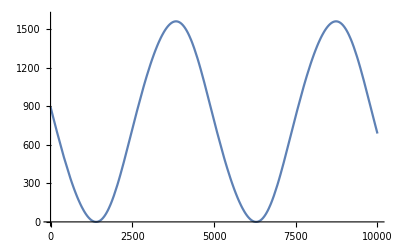

```mathematica
Plot[x[t]/.solve,{t,0,10000},PlotRange->{0,1600}]
tc=t/.FindRoot[{xc==x[t]}/.solve,{t,5000},WorkingPrecision->50];
td=t/.FindRoot[{xd==x[t]}/.solve,{t,3000},WorkingPrecision->50];
```

```mathematica
DecimalForm[ArcLength[{x[t],y[t]}/.solve,{t,td,tc},Method->{"NIntegrate",WorkingPrecision->20}]+Norm[{xc,yc}-{200,200}]+Norm[{xd,yd}-{1400,1400}],{+∞,3}]
```

2531.205

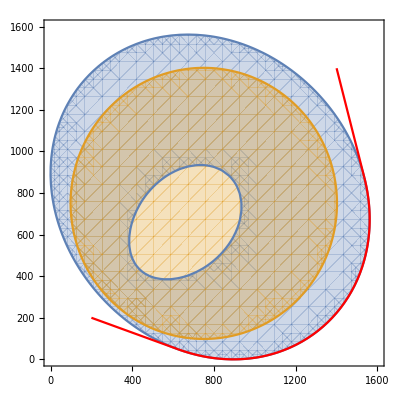

```mathematica
Show[RegionPlot[{h[x,y]≥Root[-640625000000-206250000 #1-3125 #1^2+2 #1^3&,3] ⅇ^Root[8172+56505 #1+32150 #1^2+4000 #1^3&,3],(x-750)^2+(y-750)^2<425000},{x,0,1600},{y,0,1600}],ListLinePlot[{{200,200},{xc,yc}},PlotStyle->Red],ListLinePlot[{{1400,1400},{xd,yd}},PlotStyle->Red],ParametricPlot[{x[t],y[t]}/.solve,{t,td,tc},PlotStyle->Red]]
```